# Quantum-Phase Estimation: Implementation

Episode 32. Quantum Fourier Transform: Principle

Episode 33. Quantum Fourier Transform: Implementation

Episode 34. Controlled Power

Episode 35. Quantum Phase Estimation: Principle

Episode 36. Quantum Phase Estimation: Implementation

## What to study?

Through these two episodes, one can examine the following key questions concerning quantum computing:

Why is quantum computer faster than classical computer (if at all)?

Why is it difficult to find quantum algorithms exhibiting quantum supremacy?

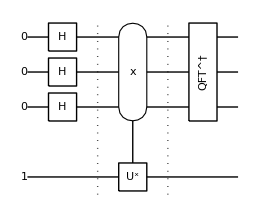

Figure 1. A schematic quantum circuit for quantum phase estimation, which illustrates the typical structure of quantum algorithms.

## Overview

```mathematica
Let[Qubit,S,T]
```

Consider a control register consisting of n qubits.

```mathematica
$n=3;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

Consider a single-qubit unitary gate acting on the target qubit.

```mathematica
Let[Real,ϕ]
opU=Phase[ϕ,T[3]]
```

Construct the controlled-power of opU defined above.

```mathematica
cop=ControlledPower[SS,opU]
```

Construct a quantum circuit for quantum phase estimation.

```mathematica
qc=QuantumCircuit[
Ket[S@kk],Ket[T->1],
S[kk,6],"Separator",
cop,"Separator",
Dagger@QFT[S[kk]],
"Invisible"->{S[$n+1/2]}
]
```

To be specific, set ϕ=(2πx)/N with N:=2^n.

```mathematica
$b={0,1,1}
$x=FromDigits[$b,2]
```

```mathematica
Block[
{ϕ=2Pi*$x/$N},
EchoTiming[out=FullSimplify@Elaborate[qc];];
ProductForm[out,{S[kk],T}]
]
```

1.01853

## Implementation on Quantum Computer

Expand the quantum circuit shown above in terms of elementary gates. Recall that
	T_k:=(1 | 0
0 | ⅇ^(ⅈπ/2^k))

```mathematica
new=Expand[qc]
```

```mathematica
Matrix[qc]-Matrix[new]//SimplifyThrough//Normal
```

## Complexity

```mathematica
Let[Qubit,S,T]
```

Consider a control register consisting of n qubits.

```mathematica
$n=4;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

```mathematica
Let[Real,ϕ]
opU=Phase[ϕ,T[3]];
cop=ControlledPower[SS,opU]
```

```mathematica
qc=QuantumCircuit[
Ket[S@kk],Ket[T->1],
S[kk,6],"Separator",
Expand@cop,"Separator",
Expand@Dagger@QFT[S[kk]],
"Invisible"->{S[$n+1/2]}
]
```

## Summary

### Keywords

Quantum supremacy, quantum superpower

Quantum super-weakness

Quantum Fourier transform

### Functions

ControlledGate

ControlledExp

QFT

### Related Links

Section 4.4 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Phase Estimation

Tutorial: Order-Finding Algorithm